## Number 1

For the isoclines, we first put
		dS/dF=(dS/dt)/(dF/dt)=(S(F-1))/(F(2-F-S))
Isoclines are the the curves for which
		(S(F-1))/(F(2-F-S))=c
for some constant c. Solving for S gives
		S=(cF(F-2))/(1-(c+1)F).
 Here are the isoclines for c=-10,-9,...,9,10 (omitting that for c=0 which is just the constant curve S=0).

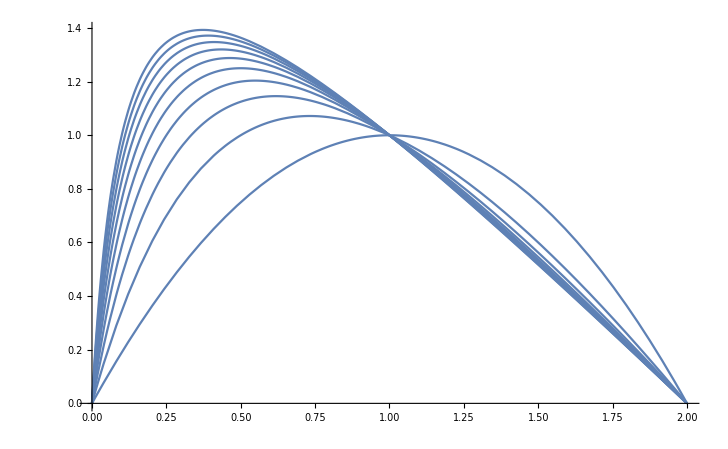
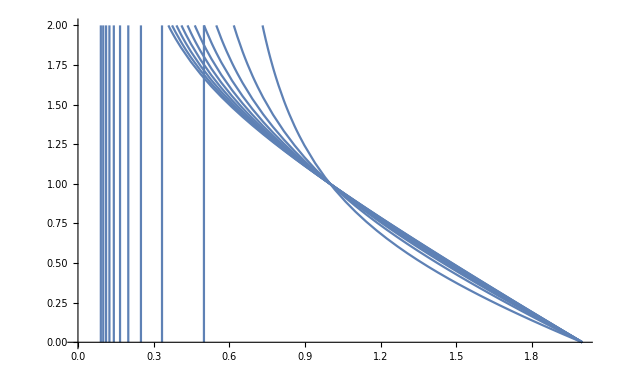

```mathematica
{Plot[Table[(2 c x-c x^2)/(-1+x+c x),{c,-10,-1}],{x,0,2}],Plot[Table[(2 c x-c x^2)/(-1+x+c x),{c,1,10}],{x,0,2},PlotRange->{0,2}]}
```

We note that the isoclines cross at (-1,1). This is possible because there is a singularity in the vector field at that point; the isoclines corresponding to given c may be better thought of as consisting of two curves than one. Here is the vector field with trajectories using StreamPlot, at two different scales.

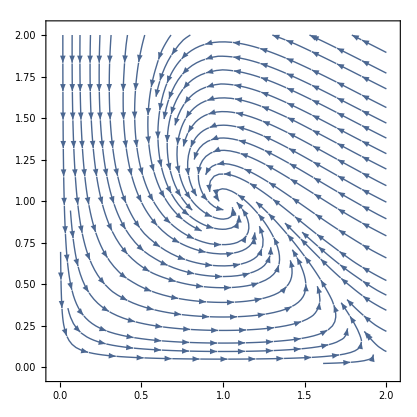
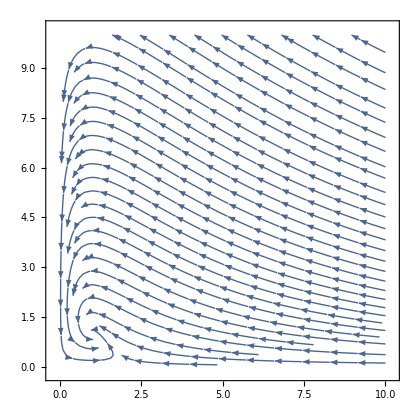

```mathematica
{StreamPlot[{x(2-x-y),y(x-1)},{x,0,2},{y,0,2}],StreamPlot[{x(2-x-y),y(x-1)},{x,0,10},{y,0,10}]}
```

We may interpret this as follows: give some number of fish and sharks (both not zero), the sharks rapidly consume the fish, increasing the shark population while decreasing the fish population. Eventually collapse of the fish population leads to collapse of the sharks as well, until the numbers settle to an equilibrium or one fish and one shark (or perhaps “one” of some index number of fish and sharks).